```mathematica
Iterated Function to get step approximation of the function
```

```mathematica
ClearAll[x]
```

```mathematica
f[x]=(2.94085*10^10)/x^12-325882/x^6
```

(2.94085×10^10)/x^12-325882/x^6

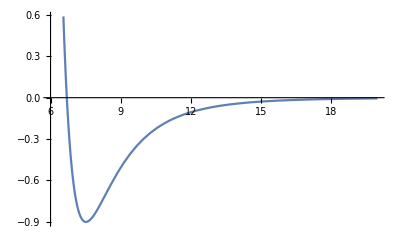

```mathematica
Plot[(2.94085*^10)/xee^12-325882/xee^6,{xee,6,20}]
```

```mathematica
(*Trying Staircase step approximation method: Feeding function into itself*)
For[xee=6.5,xee<15,xee=xee+0.1,
f[xee]=f[f[xee]]
]
```

Set::write: Tag TraditionalForm`Plus in TraditionalForm`(2.94085×10^10/x^12 - 325882/x^6)  (6.5) is Protected.

Set::write: Tag TraditionalForm`Plus in TraditionalForm`(2.94085×10^10/x^12 - 325882/x^6)  (6.6) is Protected.

Set::write: Tag TraditionalForm`Plus in TraditionalForm`(2.94085×10^10/x^12 - 325882/x^6)  (6.7) is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

```mathematica
?For
```

For[start,test,incr,body] executes start, then repeatedly evaluates body and incr until test fails to give True.

```mathematica
(* (6.69734,0) *)
```

```mathematica
NSolve[D[f[x],x]==0,x, Reals]
```

{{x→-7.51751},{x→7.51751}}

```mathematica
NSolve[D[f[xee],xee]==-1,xee, Reals]
```

{{xee→7.06619}}

```mathematica
NSolve[{D[f[x],x]==1, x≥ 7.5,x≤20},x,Reals]
```

{}

```mathematica
f[x_]=(2.94085*10^10)/x^12-325882/x^6
```

(2.94085×10^10)/x^12-325882/x^6

```mathematica
(* Finding the value of potential at minimum point *)
f[7.51751]
```

-0.902792

```mathematica
(* (x<6.69734,infinity)
(6<x<9,-0.902792)
(x>9,0) *)
```